```mathematica
Needs["OGRe`"]
```

```mathematica
TNewCoordinates["Spherical",{t,r,θ,ϕ}]
```

Spherical

```mathematica
TNewMetric["Anisotropic","Spherical",DiagonalMatrix[{-A[r],B[r],r^2,r^2 Sin[θ]^2}]]
```

TMessage::ErrorOverwrite: A tensor with the ID "Anisotropic" already exists. Please rename it using TChangeID[] or delete it using TDelete[] first. Type TSetAllowOverwrite[True] to allow overwriting tensors.

$Aborted

```mathematica
TSetReservedSymbols[M]
TNewMetric["Schwarzschild","Spherical",DiagonalMatrix[{-(1-(2 M)/r),1/(1-(2 M)/r),r^2,r^2 Sin[θ]^2}]]
```

{t,r,θ,ϕ,M}

Schwarzschild

```mathematica
TList@TCalcChristoffel["Anisotropic"]
```

TMessage::ErrorOverwrite: A tensor with the ID "AnisotropicChristoffel" already exists. Please rename it using TChangeID[] or delete it using TDelete[] first. Type TSetAllowOverwrite[True] to allow overwriting tensors.

$Aborted

```mathematica
TDelete["Phi"]
TNewTensor["Phi","Schwarzschild","Spherical",{},{ψ[r]},"ψ"]
```

Phi

```mathematica
TDelete["BoxPhi"]
TShow@TCalc["BoxPhi",TCovariantD["μ"].(TCovariantD["μ"]."Phi"[""]),"□ψ"]//FullSimplify
```

BoxPhi:   (□ψ)_^(,,trθϕ) = (2 (-M+r) Inactiveψ[r]r+r (-2 M+r) Inactiveψ[r]r^2)/r^2

```mathematica
TDelete["Box2Phi"]
TShow@TCalc["Box2Phi",TCovariantD["ν"].(TCovariantD["ν"]."BoxPhi"[""]),"□□ψ"]//FullSimplify
```

Box2Phi:   (□□ψ)_^(,,trθϕ) = (8 M (2 M-r) Inactiveψ[r]r+8 M r (-M+r) Inactiveψ[r]r^2+r^3 (-2 M+r) (4 Inactiveψ[r]r^3+(-2 M+r) Inactiveψ[r]r^4))/r^5

```mathematica
(*Solution of phi in vacuum*)
PhiVacuumEq=TGetComponents["Box2Phi"][[1]]
PhiVacuumSol=DSolve[PhiVacuumEq==0,ψ,r]//FullSimplify
```

TGetComponents::UsingDefault: Using the default index configuration {} and the default coordinate system "Spherical".

(8 M (2 M-r) ψ'[r]+8 M r (-M+r) ψ''[r]+r^3 (-2 M+r) (4 ψ^(3)[r]+(-2 M+r) ψ^(4)[r]))/r^5

{{ψ→Function[{r},C[4]-1/(12 M)(8 M^2 r C[2]+2 M r^2 C[2]-4 M r C[3]+6 C[1] Log[-2 M+r]-2 C[2] Log[-2 M+r]+16 M^3 C[2] Log[-2 M+r]-24 M^2 C[3] Log[-2 M+r]+4 M r C[3] Log[-2 M+r]+r^2 C[3] Log[-2 M+r]-8 M^2 C[3] Log[2 M-r] Log[-2 M+r]+8 M^2 C[3] Log[-2 M+r]^2-Log[r] (6 C[1]-2 C[2]+4 M r C[3]+r^2 C[3]-8 M^2 C[3] Log[2 M-r]+16 M^2 C[3] Log[1-r/(2 M)])-16 M^2 C[3] PolyLog[2,r/(2 M)])]}}

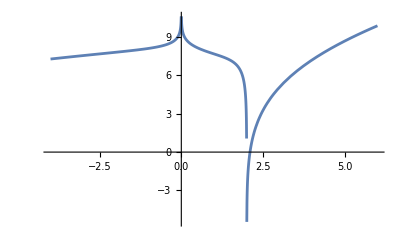

```mathematica
Plot[Evaluate[Re[ψ[r]]/. PhiVacuumSol/. {C[1]->0,C[2]->0,C[3]->1,C[4]->0,M->1}],{r,-4M,6M}/.{M->1},PlotRange->All]
```

```mathematica
(*Solution of phi in density field f(r) *)
DSolve[PhiVacuumEq==f[r],ψ,r]//FullSimplify
```

{{ψ→Function[{r},C[4]+(C[1]/((2 M-K[4]) K[4])+(C[2] (-1+K[4]^3))/(3 (2 M-K[4]) K[4])-(C[3] (M K[4] (4 M+K[4])+8 M^3 Log[2 M-K[4]]+K[4]^3 Log[K[4]]-K[4]^3 Log[-2 M+K[4]]))/(6 M (2 M-K[4]) K[4])+1/(6 M (2 M-K[4]) K[4])(-4 M^2 K[4] -f[K[3]] K[3]^2K[3]1K[4]-M K[4]^2 -f[K[3]] K[3]^2K[3]1K[4]-8 M^3 Log[2 M-K[4]] -f[K[3]] K[3]^2K[3]1K[4]-K[4]^3 Log[K[4]] -f[K[3]] K[3]^2K[3]1K[4]+K[4]^3 Log[-2 M+K[4]] -f[K[3]] K[3]^2K[3]1K[4]+6 M (-2/3 M f[K[1]] K[1]^3-1/6 f[K[1]] K[1]^4-(f[K[1]] K[1]^2 (8 M^3 Log[2 M-K[1]]+Log[K[1]]-Log[-2 M+K[1]]))/(6 M))K[1]1K[4]-2 M -(f[K[2]] K[2]^2 (Log[K[2]]-Log[-2 M+K[2]]))/(2 M)K[2]1K[4]+2 M K[4]^3 -(f[K[2]] K[2]^2 (Log[K[2]]-Log[-2 M+K[2]]))/(2 M)K[2]1K[4]))K[4]1r]}}

```mathematica
(*Solution of phi follows [2203.02803] *)
Phi2rootSol=DSolve[TGetComponents["BoxPhi"][[1]]==f[r],ψ,r]//FullSimplify
```

TGetComponents::UsingDefault: Using the default index configuration {} and the default coordinate system "Spherical".

{{ψ→Function[{r},C[2]+(ⅇ^(-2 (1/2 Log[K[2]]+1/2 Log[-2 M+K[2]])) C[1]+ⅇ^(-2 (1/2 Log[K[2]]+1/2 Log[-2 M+K[2]])) -(ⅇ^(2 (1/2 Log[K[1]]+1/2 Log[-2 M+K[1]])) f[K[1]] K[1])/(2 M-K[1])K[1]1K[2])K[2]1r]}}

```mathematica
TDelete["EnergyMomentumT"]
TList@TChangeDefaultIndices[TCalc["EnergyMomentumT",-2"BoxPhi"[""].TCovariantD["μ"]. TCovariantD["ν"]."Phi"[""]+"Schwarzschild"["μν"](1/2 "BoxPhi"[""]^2-ρ[r](1+C )"Phi"[""]),"T"],{-1,-1}]//FullSimplify
```

TMessage::ErrorDoesNotExist: The tensor "EnergyMomentumT" does not exist.

$Aborted

EnergyMomentumT:
==T_tt^tt | = | ((2 M-r) (r^4 BoxPhi[]^2-2 (1+C) r^4 Phi[] ρ[r]-4 M Inactiveψ[r]r (2 (-M+r) Inactiveψ[r]r+r (-2 M+r) Inactiveψ[r]r^2)))/(2 r^5)
==T_rr^rr | = | (-1/2 r^4 BoxPhi[]^2+(1+C) r^4 Phi[] ρ[r]-2 (2 (M-r) Inactiveψ[r]r+(2 M-r) r Inactiveψ[r]r^2) (M Inactiveψ[r]r+r (-2 M+r) Inactiveψ[r]r^2))/((2 M-r) r^3)
==T_θθ^θθ | = | 1/2 r^2 (BoxPhi[]^2-2 (1+C) Phi[] ρ[r])+(2 (2 M-r) Inactiveψ[r]r (2 (-M+r) Inactiveψ[r]r+r (-2 M+r) Inactiveψ[r]r^2))/r^2
==T_ϕϕ^ϕϕ | = | (Sin[θ]^2 (r^4 BoxPhi[]^2-2 (1+C) r^4 Phi[] ρ[r]-8 (-2 M+r) (-M+r) (Inactiveψ[r]r)^2-4 r (-2 M+r)^2 Inactiveψ[r]r Inactiveψ[r]r^2))/(2 r^2)

```mathematica
TList@TChangeDefaultIndices[TCalc["GradientT",TCovariantD["μ"]."EnergyMomentumT"["μν"],"∇T"],{1}]//FullSimplify
```

GradientT:
==(∇T)_r^r | = | ((2 M-r) ((1+C) r^5 Phi[] Inactiveρ[r]r-2 ((M-2 r) Inactiveψ[r]r+2 (2 M-r) r Inactiveψ[r]r^2) ((4 M-2 r) Inactiveψ[r]r+r^2 (2 Inactiveψ[r]r^2+(-2 M+r) Inactiveψ[r]r^3))))/r^6

```mathematica
ψ[r]=α r+β r^2;
ContinuityEq = TGetComponents["GradientT"][[2]];
ContinuitySol=DSolve[ContinuityEq==0,ρ,r]//FullSimplify
```

TGetComponents::UsingDefault: Using the default index configuration {1} and the default coordinate system "Spherical".

{{ρ→Function[{r},C[1]+1/((1+C) Phi[] K[1]^5)2 (4 M^2 ψ'[K[1]]^2-10 M K[1] ψ'[K[1]]^2+4 K[1]^2 ψ'[K[1]]^2+16 M^2 K[1] ψ'[K[1]] ψ''[K[1]]-14 M K[1]^2 ψ'[K[1]] ψ''[K[1]]+8 M K[1]^3 ψ''[K[1]]^2-4 K[1]^4 ψ''[K[1]]^2-2 M^2 K[1]^2 ψ'[K[1]] ψ^(3)[K[1]]+5 M K[1]^3 ψ'[K[1]] ψ^(3)[K[1]]-2 K[1]^4 ψ'[K[1]] ψ^(3)[K[1]]-8 M^2 K[1]^3 ψ''[K[1]] ψ^(3)[K[1]]+8 M K[1]^4 ψ''[K[1]] ψ^(3)[K[1]]-2 K[1]^5 ψ''[K[1]] ψ^(3)[K[1]])K[1]1r]}}

```mathematica
TList@TCalcEinsteinTensor["Anisotropic"]
```

AnisotropicEinstein:
==G_tt^tt | = | (A[t,r] ((-1+B[t,r]) B[t,r]+r InactiveB[t,r]r))/(r^2 B[t,r]^2)
==G_tr^trG_rt^rt | = | (InactiveB[t,r]t)/(r B[t,r])
==G_rr^rr | = | (1-B[t,r]+(r InactiveA[t,r]r)/A[t,r])/r^2
==G_θθ^θθ | = | (r (-2 A[t,r]^2 InactiveB[t,r]r+r B[t,r] (-(InactiveA[t,r]r)^2+InactiveA[t,r]t InactiveB[t,r]t)+A[t,r] (r (-InactiveA[t,r]r InactiveB[t,r]r+(InactiveB[t,r]t)^2)+2 B[t,r] (InactiveA[t,r]r+r InactiveA[t,r]r^2-r InactiveB[t,r]t^2))))/(4 A[t,r]^2 B[t,r]^2)
==G_ϕϕ^ϕϕ | = | (r Sin[θ]^2 (-2 A[t,r]^2 InactiveB[t,r]r+r B[t,r] (-(InactiveA[t,r]r)^2+InactiveA[t,r]t InactiveB[t,r]t)+A[t,r] (r (-InactiveA[t,r]r InactiveB[t,r]r+(InactiveB[t,r]t)^2)+2 B[t,r] (InactiveA[t,r]r+r InactiveA[t,r]r^2-r InactiveB[t,r]t^2))))/(4 A[t,r]^2 B[t,r]^2)